```mathematica
Slovenija Plin
```

```mathematica
data=Import[NotebookDirectory[]<> "cene_urejena.csv", "Table", FieldSeparators -> ",", HeaderLines -> 2, CharacterEncoding->"WindowsEastEurope"]//Transpose//ResourceFunction["DatasetWithHeaders"]
```

Dataset[<>]

čiščenje podatkov tako da odstranimo enoto ter ceno

```mathematica
D1= data //
Query[3;;, {1,2}]
```

Dataset[<>]

```mathematica
dat12=D1//Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]
```

Dataset[<>]

```mathematica
opvprečja obdobja
```

```mathematica
opvprečjaobdobja=dat12//
Query[GroupBy[#obdobje&]/*Values,<|
"obdobje"-> Query[First,"obdobje"],
"opovprečjeD1"->Query[Mean,"D1 (< 20 GJ)"]
|>]
```

Dataset[<>]

```mathematica
PieChart[opvprečjaobdobja//Query[All,2],ChartLegends->{Q1,Q2,Q3,Q4}]
```

-Graphics-

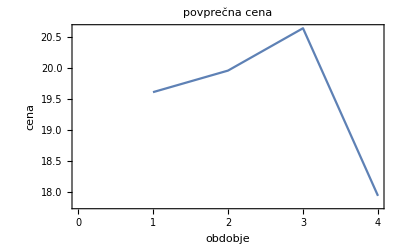

```mathematica
ListLinePlot[opvprečjaobdobja//Query[All,2],
PlotLabel->"povprečna cena", 
FrameLabel->{ "obdobje", "cena"}, 
Frame-> {{True, False}, {True, False}}
]
```

```mathematica
povprečje leta
```

```mathematica
povprečnaleto=dat12//
Query[GroupBy[#leto&]/*Values,<|
"leto"-> Query[First,"leto"],
"povprecje"->Query[Mean,"D1 (< 20 GJ)"]

|>
]
```

Dataset[<>]

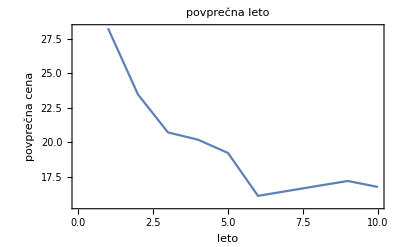

```mathematica
ListLinePlot[povprečnaleto//Query[All,2],
PlotLabel->"povprečna leto", 
FrameLabel->{ "leto", "povprečna cena"}, 
Frame-> {{True, False}, {True, False}}
]
```

povprečna leto

```mathematica
grupl=GroupBy[dat12//Query[All,All],"leto"]
```

Dataset[<>]

```mathematica
grupl1=grupl["2012"]
```

Dataset[<>]

```mathematica
leto2012=grupl1//Query[All,{2,3}]
```

Dataset[<>]

```mathematica
poglejpoletih[x_]:=grupl[x]//Query[All,3]//******
ListLinePlot[
#, 
PlotLabel->"graf za leto x", 
FrameLabel->{ "Leto", "Število vpisanih"}, 
Frame-> {{True, False}, {True, False}}
]&
```

obdobja čez leto,,,obdobja čez leta,,, povprečna cena leta,,,povprečnacena obdobja

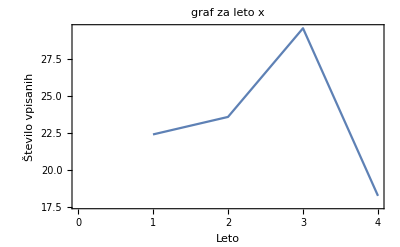

```mathematica
poglejpoletih["2013"]
```

```mathematica
1=D1
2=D2
3=D3
4=Slovenija
```

```mathematica
funkcijaextra[D_,leto_]:=data //Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]//
GroupBy[#//Query[All,All],"leto"]&//
#[leto]&//
Query[All,{2,3}]//********
ListLinePlot[
#, 
PlotLabel->"graf za leto x", 
FrameLabel->{ "Leto", "Število vpisanih"}, 
Frame-> {{True, False}, {True, False}}
]&
```

```mathematica
funkcijaextra[1,"2013"]
```

-Graphics-